### Declare Test Set

```mathematica
CreateTestFunction[name_, def_, x0_] := <|"Name" -> name, "Definition" -> def, "x0" -> x0|>;

TestSet = { 
	CreateTestFunction[
	    "genrose",
	    Function[x,
	    Module[{n = Length[x]},
	        1 + 
	        100 * Sum[(x[[i + 1]] - x[[i]]^2)^2, {i, 1, n - 1}] + 
	        Sum[(x[[i]] - 1)^2, {i, 1, n - 1}]
	    ]],
	    Function[n, N[Table[i/(n + 1), {i, 1, n}]]]
	],
	CreateTestFunction[
	    "arglina",
	    Function[x, Module[{n = Length[x], m, sj},
	        m = 2*n;
	        sj = Total[x];
	        (1/2)*Sum[(x[[i]] - (2/m)*sj - 1)^2, {i, n}] +
	        (1/2)*Sum[(-(2/m)*sj - 1)^2, {i, n+1, m}]
	    ]],
	    Function[n, ConstantArray[1, n]]
	],
	CreateTestFunction[
	    "freuroth",
	    Function[x,
	    Module[{n = Length[x]},
	        (1/2) * Sum[((5 - x[[i + 1]])*x[[i + 1]]^2 + x[[i]] - 2*x[[i + 1]] - 13)^2, {i, 1, n - 1}] +
	        (1/2) * Sum[((1 + x[[i + 1]])*x[[i + 1]]^2 + x[[i]] - 14*x[[i + 1]] - 29)^2, {i, 1, n - 1}]
	    ]],
	    Function[n,
	    Module[{x0 = ConstantArray[0, n]},
	        x0[[1]] = 1/2;
	        x0[[2]] = -2;
	        x0
	    ]]
	],
	CreateTestFunction[
	    "eg2",
	    Function[x,
	    Module[{n = Length[x]},
	        Sum[Sin[x[[1]] + x[[i]]^2 - 1], {i, 1, n - 1}] + (1/2)*Sin[x[[n]]^2]
	    ]],
	    Function[n, ConstantArray[0, n]]
	],
	CreateTestFunction[
	    "brybnd",
	    Function[x,
	    Module[{n = Length[x], ml = 5, mu = 1},
	        (1/2) * Sum[
	            (
	                x[[i]] * (2 + 5 * x[[i]]^2) + 1 -
	                Sum[If[j != i, x[[j]] * (1 + x[[j]]), 0], {j, Max[1, i - ml], Min[n, i + mu]}]
	            )^2,
	            {i, 1, n}
	        ]
	    ]],
	    Function[n, -ConstantArray[1, n]]
	],
    CreateTestFunction[
        "cosine",
        Function[x,
        Module[{n = Length[x]},
            Sum[Cos[x[[i]]^2 - x[[i + 1]]/2], {i, 1, n - 1}]
        ]],
        Function[n, ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "arglinb",
        Function[x,
        Module[{n = Length[x], m, sj},
            m = 2*n;
            sj = Sum[j*x[[j]], {j, 1, n}];
            (1/2)*Sum[(i*sj - 1)^2, {i, 1, m}]
        ]],
        Function[n, ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "arglinc",
        Function[x, 
        Module[{n = Length[x], m, sj},
            m = 2*n;
            sj = Sum[j*x[[j]], {j, 2, n - 1}];
            2 + Sum[((i - 1)*sj - 1)^2, {i, 2, m - 1}]
        ]],
        Function[n, ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "argtrig",
        Function[x,
        Module[{n = Length[x]},
            n - Sum[Cos[x[[j]]] + j*(1 - Cos[x[[j]]]) - Sin[x[[j]]], {j, 1, n}]
        ]],
        Function[n, ConstantArray[1/n, n]]
    ],
    CreateTestFunction[
        "arwhead",
        Function[x,
        Module[{n = Length[x]},
            Sum[(x[[i]]^2 + x[[n]]^2)^2 - 4*x[[i]] + 3, {i, 1, n - 1}]
        ]],
        Function[n, ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "bdqrtic",
        Function[x,
        Module[{n = Length[x]},
            (1/2) * Sum[
                (3 - 4*x[[i]])^2 + (x[[i]]^2 + 2*x[[i + 1]]^2 + 3*x[[i + 2]]^2 + 4*x[[i + 3]]^2 + 5*x[[n]]^2)^2,
                {i, 1, n - 4}
            ]
        ]],
        Function[n, ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "brownal",
        Function[x,
        Module[{n = Length[x], sj, pj},
            sj = Total[x];
            pj = Times @@ x;
            (1/2) * Sum[(x[[i]] + sj - (n + 1))^2, {i, 1, n - 1}] + (1/2) * (pj - 1)^2
        ]],
        Function[n, ConstantArray[1/2, n]]
    ],
    CreateTestFunction[
        "broyden3d",
        Function[x, 
        Module[{n = Length[x]},
            (1/2) * Sum[((3 - 2*x[[i]])*x[[i]] - x[[i - 1]] - 2*x[[i + 1]] + 1)^2, {i, 2, n - 1}] +
            (1/2) * ((3 - 2*x[[1]])*x[[1]] - 2*x[[2]] + 1)^2 +
            (1/2) * ((3 - 2*x[[n]])*x[[n]] - x[[n - 1]] + 1)^2
        ]],
        Function[n, -ConstantArray[1, n]]
    ],
	CreateTestFunction[
	    "brybnd",
	    Function[x,
	    Module[{n = Length[x], ml = 5, mu = 1},
	        (1/2) * Sum[
	            (
	                x[[i]] * (2 + 5 * x[[i]]^2) + 1 -
	                Sum[If[j != i, x[[j]] * (1 + x[[j]]), 0], {j, Max[1, i - ml], Min[n, i + mu]}]
	            )^2,
	            {i, 1, n}
	        ]
	    ]],
	    Function[n, -ConstantArray[1, n]]
	],
	 CreateTestFunction[
	    "chnrosnb_mod",
	    Function[x,
	    Module[{n = Length[x]},
	        16 * Sum[
	            (x[[i - 1]] - x[[i]]^2)^2 * (15/10 + Sin[i])^2,
	            {i, 2, n}
	        ] +
	        Sum[(1 - x[[i]])^2, {i, 2, n}]
	    ]],
	    Function[n, -ConstantArray[1, n]]
	],
    CreateTestFunction[
        "cragglvy",
        Function[x,
        Module[{n = Length[x]},
            Sum[
                (Exp[x[[2*i - 1]]] - x[[2*i]])^4 +
                100*(x[[2*i]] - x[[2*i + 1]])^6 +
                (Tan[x[[2*i + 1]] - x[[2*i + 2]]] + x[[2*i + 1]] - x[[2*i + 2]])^4 +
                x[[2*i - 1]]^8 +
                (x[[2*i + 2]] - 1)^2,
                {i, 1, Floor[n/2] - 1}
            ]
        ]],
        Function[n,
        Module[{x0 = Join[{1}, ConstantArray[2, n - 1]]},
            x0
        ]]
    ],
    CreateTestFunction[
        "cragglvy2",
        Function[x,
        Module[{n = Length[x]},
            Sum[
                (Exp[x[[2*i - 1]]] - x[[2*i]])^4 +
                100*(x[[2*i]] - x[[2*i + 1]])^6 +
                (Tan[x[[2*i + 1]] - x[[2*i + 2]]])^4 +
                x[[2*i - 1]]^8 +
                (x[[2*i + 2]] - 1)^2,
                {i, 1, Floor[n/2] - 1}
            ]
        ]],
        Function[n,
        Join[{1}, ConstantArray[2, n - 1]]
        ]
    ],
    CreateTestFunction[
        "curly10",
        Function[x,
        Module[{n = Length[x], b = 10},
            Sum[
                Module[{s = Total[Table[x[[j]], {j, i, Min[i + b, n]}]]},
                    s * (s * (s^2 - 20) - (1/10))
                ],
                {i, 1, n}
            ]
        ]],
        Function[n, Table[1.0*10^-4 * i / (n + 1), {i, 1, n}]]
    ],
    CreateTestFunction[
        "curly10",
        Function[x,
        Module[{n = Length[x], b = 10},
            Sum[
                Module[{s = Sum[x[[j]], {j, i, Min[i + b, n]}]},
                    s * (s * (s^2 - 20) - 1/10)
                ],
                {i, 1, n}
            ]
        ]],
        Function[n, Table[1.0*10^-4*i/(n + 1), {i, n}]]
    ],
    CreateTestFunction[
        "curly20",
        Function[x, 
        Module[{n = Length[x], b = 20}, 
            Sum[
                Module[{s = Sum[x[[j]], {j, i, Min[i + b, n]}]}, 
                    s * (s * (s^2 - 20) - (1/10))
                ], 
                {i, 1, n}
            ]
        ]],
        Function[n, Table[1.0*10^-4 * i/(n + 1), {i, n}]]
    ],
    CreateTestFunction[
        "curly30",
        Function[x,
        Module[{n = Length[x], b = 30},
            Sum[
                Module[{s = Sum[x[[j]], {j, i, Min[i + b, n]}]},
                    s * (s * (s^2 - 20) - 1/10)
                ],
                {i, 1, n}
            ]
        ]],
        Function[n, Table[1.0*10^-4*i/(n + 1), {i, n}]]
    ],
    CreateTestFunction[
        "dixon3dq",
        Function[x,
        Module[{n = Length[x]},
            (1/2)*(x[[1]] - 1)^2 + 
            (1/2)*(x[[n]] - 1)^2 + 
            (1/2)*Sum[(x[[i]] - x[[i + 1]])^2, {i, 2, n - 1}]
        ]],
        Function[n, -ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "dqdrtic",
        Function[x,
        Module[{n = Length[x]},
            Sum[x[[i]]^2 + 100*(x[[i + 1]]^2 + x[[i + 2]]^2), {i, 1, n - 2}]
        ]],
        Function[n, 3 * ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "dqrtic",
        Function[x,
        Module[{n = Length[x]},
            Sum[(x[[i]] - i)^4, {i, 1, n}]
        ]],
        Function[n, 2 * ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "edensch",
        Function[x,
        Module[{n = Length[x]},
            16 + Sum[
                (x[[i]] - 2)^4 + (x[[i]]*x[[i + 1]] - 2*x[[i + 1]])^2 + (x[[i + 1]] + 1)^2,
                {i, 1, n - 1}
            ]
        ]],
        Function[n, ConstantArray[0, n]]
    ],
    CreateTestFunction[
        "eg2",
        Function[x,
        Module[{n = Length[x]},
            Sum[Sin[x[[1]] + x[[i]]^2 - 1], {i, 1, n - 1}] + (1/2)*Sin[x[[n]]^2]
        ]],
        Function[n, ConstantArray[0, n]]
    ],
    CreateTestFunction[
        "engval1",
        Function[x,
        Module[{n = Length[x]},
            Sum[(x[[i]]^2 + x[[i + 1]]^2)^2 - 4*x[[i]] + 3, {i, 1, n - 1}]
        ]],
        Function[n, ConstantArray[2, n]]
    ],
    CreateTestFunction[
        "errinros_mod",
        Function[x,
        Module[{n = Length[x]},
            (1/2) * Sum[(x[[i - 1]] - 16*x[[i]]^2*(3/2 + Sin[i])^2)^2, {i, 2, n}] +
            (1/2) * Sum[(1 - x[[i]])^2, {i, 2, n}]
        ]],
        Function[n, -ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "extrosnb",
        Function[x, 
        Module[{n = Length[x]}, 
            100 * Sum[(x[[i]] - x[[i - 1]]^2)^2, {i, 2, n}] + (1 - x[[1]])^2
        ]],
        Function[n, -ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "fletcbv2",
        Function[x,
        Module[{n = Length[x], h},
            h = 1/(n + 1);
            (1/2) * (x[[1]]^2 + Sum[(x[[i]] - x[[i + 1]])^2, {i, 1, n - 1}] + x[[n]]^2) - 
            h^2 * Sum[2*x[[i]] + Cos[x[[i]]], {i, 1, n}] - x[[n]]
        ]],
        Function[n, Table[i/(n + 1), {i, 1, n}]]
    ],
    CreateTestFunction[
        "fletcbv3_mod",
        Function[x,
        Module[{n = Length[x], p, h},
            p = 1/100000000;
            h = 1/(n + 1);
            (p/2) * (x[[1]]^2 + Sum[(x[[i]] - x[[i + 1]])^2, {i, 1, n - 1}] + x[[n]]^2) - 
            p * Sum[100 * (1 + (2/h^2)) * Sin[x[[i]]/100] + (1/h^2) * Cos[x[[i]]], {i, 1, n}]
        ]],
        Function[n, Table[i/(n + 1), {i, 1, n}]]
    ],
    CreateTestFunction[
        "fletchcr",
        Function[x,
        Module[{n = Length[x]},
            100 * Sum[(x[[i + 1]] - x[[i]] + 1 - x[[i]]^2)^2, {i, 1, n - 1}]
        ]],
        Function[n, ConstantArray[0, n]]
    ],
    CreateTestFunction[
        "freuroth",
        Function[x,
        Module[{n = Length[x]},
            (1/2) * Sum[((5 - x[[i + 1]])*x[[i + 1]]^2 + x[[i]] - 2*x[[i + 1]] - 13)^2, {i, 1, n - 1}] +
            (1/2) * Sum[((1 + x[[i + 1]])*x[[i + 1]]^2 + x[[i]] - 14*x[[i + 1]] - 29)^2, {i, 1, n - 1}]
        ]],
        Function[n,
        Module[{x0 = ConstantArray[0, n]},
            x0[[1]] = 1/2;
            x0[[2]] = -2;
            x0
        ]]
    ],
    CreateTestFunction[
        "genhumps",
        Function[x,
        Module[{n = Length[x], ζ = 20},
            Sum[
                Sin[ζ*x[[i]]]^2 * Sin[ζ*x[[i + 1]]]^2 + (5/100) * (x[[i]]^2 + x[[i + 1]]^2),
                {i, 1, n - 1}
            ]
        ]],
        Function[n,
        Module[{x0 = -506.2*ConstantArray[1, n]},
            x0[[1]] = -506;
            x0
        ]]
    ],
    CreateTestFunction[
        "genrose_nash",
        Function[x, 
        Module[{n = Length[x]},
            1 + 100 * Sum[(x[[i]] - x[[i - 1]]^2)^2, {i, 2, n}] + 
            Sum[(1 - x[[i]])^2, {i, 2, n}]
        ]],
        Function[n, Table[i / (n + 1), {i, 1, n}]]
    ],
    CreateTestFunction[
        "indef_mod",
        Function[x,
        Module[{n = Length[x]},
            100 * Sum[Sin[x[[i]] / 100], {i, 1, n}] +
            (1/2) * Sum[Cos[2 * x[[i]] - x[[n]] - x[[1]]], {i, 2, n - 1}]
        ]],
        Function[n, Table[i / (n + 1), {i, 1, n}]]
    ],
    CreateTestFunction[
        "integreq",
        Function[x,
        Module[{n = Length[x], h},
            h = 1/(n + 1);
            (1/2) * Sum[
                (
                    x[[i]] + 
                    h * (
                        (1 - i*h) * Sum[j*h*(x[[j]] + j*h + 1)^3, {j, 1, i}] + 
                        i*h * Sum[(1 - j*h)*(x[[j]] + j*h + 1)^3, {j, i + 1, n}]
                    ) / 2
                )^2, {i, 1, n - 1}
            ] + 
            (1/2) * (
                x[[n]] + 
                h * ((1 - n*h) * Sum[j*h*(x[[j]] + j*h + 1)^3, {j, 1, n}]) / 2
            )^2
        ]],
        Function[n,
        Module[{x0},
            x0 = Table[j * (1/(n + 1)) * (j * (1/(n + 1)) - 1), {j, 1, n}];
            x0
        ]]
    ],
    CreateTestFunction[
        "liarwhd",
        Function[x,
        Module[{n = Length[x]},
            Sum[4*(x[[i]]^2 - x[[1]])^2 + (x[[i]] - 1)^2, {i, 1, n}]
        ]],
        Function[n, 4*ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "morebv",
        Function[x,
        Module[{n = Length[x], h},
            h = 1/(n + 1);
            (1/2) * Sum[
                (2*x[[i]] - x[[i - 1]] - x[[i + 1]] + (h^2/2)*(x[[i]] + i*h + 1)^3)^2,
                {i, 2, n - 1}
            ] +
            (1/2) * (2*x[[1]] - x[[2]] + (h^2/2)*(x[[1]] + 1)^3)^2 +
            (1/2) * (2*x[[n]] - x[[n - 1]] + (h^2/2)*(x[[n]] + n*h + 1)^3)^2
        ]],
        Function[n, ConstantArray[1/2, n]]
    ],
	CreateTestFunction[
	    "noncvxu2",
	    Function[x,
	        Module[{n = Length[x]},
	            Sum[
	                ( x[[i]] 
	                  + x[[Mod[3*i - 2, n] + 1]] 
	                  + x[[Mod[7*i - 3, n] + 1]] 
	                )^2 
	                + 4 * Cos[
	                    x[[i]] 
	                    + x[[Mod[3*i - 2, n] + 1]] 
	                    + x[[Mod[7*i - 3, n] + 1]]
	                ],
	                {i, 1, n}
	            ]
	        ]
	    ],
	    Function[n, N[Range[n]]]
	],
	CreateTestFunction[
	    "noncvxun",
	    Function[x,
	        Module[{n = Length[x]},
	            Sum[
	                ( x[[i]]
	                  + x[[Mod[2*i - 1, n] + 1]]
	                  + x[[Mod[3*i - 1, n] + 1]]
	                )^2
	                + 4 * Cos[
	                    x[[i]]
	                    + x[[Mod[2*i - 1, n] + 1]]
	                    + x[[Mod[3*i - 1, n] + 1]]
	                ],
	                {i, 1, n}
	            ]
	        ]
	    ],
	    Function[n, N[Range[n]]]
	],
    CreateTestFunction[
        "nondia",
        Function[x, 
        Module[{n = Length[x]}, 
            (x[[1]] - 1)^2 + 100 * Sum[(x[[1]] - x[[i]]^2)^2, {i, 2, n}]
        ]],
        Function[n, -ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "nondquar",
        Function[x,
        Module[{n = Length[x]},
            (x[[1]] - x[[2]])^2 + (x[[n - 1]] - x[[n]])^2 + 
            Sum[(x[[i]] + x[[i + 1]] + x[[n]])^4, {i, 1, n - 2}]
        ]],
        Function[n,
        Module[{x0 = ConstantArray[1, n]},
            Do[x0[[2*i]] = -1, {i, 1, Floor[n/2]}];
            x0
        ]]
    ],
    CreateTestFunction[
        "penalty1",
        Function[x,
        Module[{n = Length[x], a = Sqrt[1*10^-5]},
            (1/2) * Sum[(a * (x[[i]] - 1))^2, {i, 1, n}] +
            (1/2) * (Sum[x[[j]]^2, {j, 1, n}] - 1/4)^2
        ]],
        Function[n, Table[j, {j, 1, n}]]
    ],
    CreateTestFunction[
        "penalty2",
        Function[x,
        Module[{n = Length[x], a = 1/100000, m, y},
            m = 2*n;
            y = Table[Exp[i/10] + Exp[(i - 1)/10], {i, m}];
            (x[[1]] - 2/10)^2 +
            Sum[a*(Exp[x[[i]]/10] + Exp[x[[i - 1]]/10] - y[[i]])^2, {i, 2, n}] +
            Sum[a*(Exp[x[[i - n + 1]]/10] - Exp[-1/10])^2, {i, n + 1, 2*n - 1}] +
            (Sum[(n - j + 1)*x[[j]]^2, {j, 1, n}] - 1)^2
        ]],
        Function[n, ConstantArray[1/2, n]]
    ],
    CreateTestFunction[
        "penalty3",
        Function[x,
        Module[{n = Length[x]},
            1 +
            Sum[(x[[i]] - 1)^2, {i, 1, Floor[n/2]}] +
            Exp[x[[n]]] * Sum[(x[[i]] + 2*x[[i + 1]] + 10*x[[i + 2]] - 1)^2, {i, 1, n - 2}] +
            Sum[(x[[i]] + 2*x[[i + 1]] + 10*x[[i + 2]] - 1)^2, {i, 1, n - 2}] *
            Sum[(2*x[[i]] + x[[i + 1]] - 3)^2, {i, 1, n - 2}] +
            Exp[x[[n - 1]]] * Sum[(2*x[[i]] + x[[i + 1]] - 3)^2, {i, 1, n - 2}] +
            (Sum[x[[i]]^2 - n, {i, 1, n}])^2
        ]],
        Function[n, Table[i/(n + 1), {i, 1, n}]]
    ],
    CreateTestFunction[
        "power",
        Function[x,
        Module[{n = Length[x]},
            (1/2) * (Sum[i * x[[i]]^2, {i, 1, n}])^2
        ]],
        Function[n, ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "quartc",
        Function[x,
        Module[{n = Length[x]},
            Sum[(x[[i]] - i)^4, {i, 1, n}]
        ]],
        Function[n, 2 * ConstantArray[1, n]]
    ],
	CreateTestFunction[
	    "sbrybnd",
	    Function[x,
	    Module[{n = Length[x], p, J},
	        p = Table[Exp[6 * (i - 1)/(n - 1)], {i, 1, n}];
	        J = Table[Join[Range[Max[1, i - 5], i - 1], Range[i + 1, Min[n, i + 1]]], {i, 1, n}];
	        (1/2) * Sum[
	            (
	                (2 + 5 * p[[i]]^2 * x[[i]]^2) * p[[i]] * x[[i]] + 1 -
	                Sum[p[[j]] * x[[j]] * (1 + p[[j]] * x[[j]]), {j, J[[i]]}]
	            )^2,
	            {i, 1, n}
	        ]
	    ]],
	    Function[n,
	    Module[{p, x0},
	        p = Table[Exp[6 * (i - 1)/(n - 1)], {i, 1, n}];
	        x0 = Table[1/p[[i]], {i, 1, n}];
	        x0
	    ]]
	],
    CreateTestFunction[
        "schmvett",
        Function[x,
        Module[{n = Length[x]},
            Sum[
                -(1/(1 + (x[[i]] - x[[i + 1]])^2)) - Sin[(Pi*x[[i + 1]] + x[[i + 2]])/2] -
                Exp[-((x[[i]] + x[[i + 2]])/x[[i + 1]] - 2)^2],
            {i, 1, n - 2}
            ]
        ]],
        Function[n, 3*ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "scosine",
        Function[x,
        Module[{n = Length[x], p},
            p = Table[Exp[6*(i - 1)/(n - 1)], {i, 1, n}];
            Sum[Cos[p[[i]]^2*x[[i]]^2 - (p[[i + 1]]*x[[i + 1]])/2], {i, 1, n - 1}]
        ]],
        Function[n,
        Module[{p, x0},
            p = Table[Exp[6*(i - 1)/(n - 1)], {i, 1, n}];
            x0 = Table[1/p[[i]], {i, 1, n}];
            x0
        ]]
    ],
    CreateTestFunction[
        "sinquad",
        Function[x,
        Module[{n = Length[x]},
            (x[[1]] - 1)^4 +
            (x[[n]]^2 - x[[1]]^2)^2 +
            Sum[(Sin[x[[i]] - x[[n]]] - x[[1]]^2 + x[[i]]^2)^2, {i, 2, n - 1}]
        ]],
        Function[n, ConstantArray[1/10, n]]
    ],
    CreateTestFunction[
        "tointgss",
        Function[x,
        Module[{n = Length[x]},
            Sum[
                ((10/(n + 2)) + x[[i + 2]]^2) * (2 - Exp[-(x[[i]] - x[[i + 1]])^2 / (1/10 + x[[i + 2]]^2)]),
                {i, 1, n - 2}
            ]
        ]],
        Function[n, 3 * ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "tquartic",
        Function[x,
        Module[{n = Length[x]},
            (1/2) * (x[[1]] - 1)^2 + (1/2) * Sum[(x[[1]]^2 - x[[i + 1]]^2)^2, {i, 1, n - 2}]
        ]],
        Function[n, 0.1 * ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "tridia",
        Function[x,
        Module[{n = Length[x]},
            (x[[1]] - 1)^2 + Sum[i*(-x[[i - 1]] + 2*x[[i]])^2, {i, 2, n}]
        ]],
        Function[n, ConstantArray[1, n]]
    ],
    CreateTestFunction[
        "vardim",
        Function[x,
        Module[{n = Length[x]},
            Sum[(x[[i]] - 1)^2, {i, 1, n}] +
            Sum[i * (x[[i]] - 1), {i, 1, n}]^2 +
            Sum[i * (x[[i]] - 1), {i, 1, n}]^4
        ]],
        Function[n, Table[1 - i/n, {i, 1, n}]]
    ]
};
```

```mathematica
Length[TestSet]
problemNames=Table[TestSet[[i,"Name"]],{i,1,Length[TestSet]}]
(*Export["~/Desktop/numerical-optimization/public/test-problems.json", problemNames, "JSON"]*)
```

56

{genrose,arglina,freuroth,eg2,brybnd,cosine,arglinb,arglinc,argtrig,arwhead,bdqrtic,brownal,broyden3d,brybnd,chnrosnb_mod,cragglvy,cragglvy2,curly10,curly10,curly20,curly30,dixon3dq,dqdrtic,dqrtic,edensch,eg2,engval1,errinros_mod,extrosnb,fletcbv2,fletcbv3_mod,fletchcr,freuroth,genhumps,genrose_nash,indef_mod,integreq,liarwhd,morebv,noncvxu2,noncvxun,nondia,nondquar,penalty1,penalty2,penalty3,power,quartc,sbrybnd,schmvett,scosine,sinquad,tointgss,tquartic,tridia,vardim}

#### We demonstrate/test our analysis with the Generalized Rosenbrock

```mathematica
rosen=First[Select[TestSet,#["Name"]==="genrose"&]];
rosenf[x_]:=rosen["Definition"][x];
```

We reconstruct the standard contour plot, ref: https://en.wikipedia.org/wiki/Rosenbrock_function
Notice that our starting location is correct, and the generalized Rosenbrock should not be confused with the standard  “srosenbr”, which starts at  (-1.2, 1), i.e. the top left side of the banana.

```mathematica
(*Define the known minimum and initial iterate points*)
minPoint={1,1};
initialPoint=rosen["x0"][2];

GraphicsRow[{ContourPlot[rosenf[{x1,x2}],{x1,-2,2},{x2,-1,3},Contours->50,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"x₁","x₂"},PlotLabel->"Contour Plot of the Rosenbrock Function",Epilog->{Red,PointSize[0.02],Point[minPoint],Text[Style["Minimum",14,Bold,Black],minPoint+{0,0.1}],Blue,PointSize[0.02],Point[initialPoint],Text[Style["Initial",14,Bold,Black],initialPoint+{0,0.1}]},ImageSize->400],Show[Plot3D[rosenf[{x1,x2}],{x1,-2,2},{x2,-1,3},ColorFunction->"Rainbow",Mesh->None,PlotLegends->Automatic,AxesLabel->{"x₁","x₂","f(x₁, x₂)"},PlotLabel->"3D Surface Plot of the Rosenbrock Function",PlotRange->All,ImageSize->400],Graphics3D[{
Red,PointSize[0.02],Point[{minPoint[[1]],minPoint[[2]],rosenf[minPoint]}],Text[Style["Minimum",14,Bold,Black],{minPoint[[1]],minPoint[[2]],rosenf[minPoint]},{0,1}],
Blue,PointSize[0.02],Point[{initialPoint[[1]],initialPoint[[2]],rosenf[initialPoint]}],Text[Style["Initial",14,Bold,Black],{initialPoint[[1]],initialPoint[[2]],rosenf[initialPoint]},{0,1}]
}]
]}]
```

-Graphics-

## Testing

### Initial Iterate Export

For each problem in our TestSet, we compute f(x0) in dimension  5, 6, 7, 10, and 15.

 We choose 5 to be the minimum dimension that we will consider, as “bdqrtic”’s minimum dimension is 5. Other problems in our test set are constrained in dimension.

```mathematica
InitialValue[testFunction_, n_] := Module[
	{x0, f},
	x0 = testFunction["x0"][n];
	<|
		"Name" -> testFunction["Name"],
		"InitialValue" -> N[testFunction["Definition"][x0]]
	|>
];
Export["~/Desktop/numerical-optimization/public/fx0-dim5-mathematica.json", Map[InitialValue[#, 5]&, TestSet], "JSON"];
Export["~/Desktop/numerical-optimization/public/fx0-dim6-mathematica.json", Map[InitialValue[#, 6]&, TestSet], "JSON"];
Export["~/Desktop/numerical-optimization/public/fx0-dim7-mathematica.json", Map[InitialValue[#, 7]&, TestSet], "JSON"];
Export["~/Desktop/numerical-optimization/public/fx0-dim10-mathematica.json", Map[InitialValue[#, 10]&, TestSet], "JSON"];
Export["~/Desktop/numerical-optimization/public/fx0-dim15-mathematica.json", Map[InitialValue[#, 15]&, TestSet], "JSON"];
```

## Problem Investigation

We are using Mathematica to leverage the symbolic expressions for f(x) and ∇^2 f(x):

```mathematica
BuildGradAndHess[f_, n_]:= Module[
	{i, var, df, ddf},
	var=Array[x,n];
	df=D[f[var],{var}];
	ddf=D[f[var],{var,2}];
	Quiet[{
		Function[Evaluate[x],Evaluate[df/.x[i_]:>Part[x,i]]],
		Function[Evaluate[x],Evaluate[ddf/.x[i_]:>Part[x,i]]]
	}]
];
```

### Motivating Illustration

A useful test  is to perform gradient descent and newton’s method,
note, these methods respectively give us a worst and best bound on what 
we may expect from a QN descent.

```mathematica
(*Use BuildGradAndHess to compute gradient and Hessian functions*)(*Example definition of rosenf to ensure numeric evaluation*)rosenf[{x_,y_}]:=rosen["Definition"][{x,y}]
rosenf[x_,y_]:=rosenf[{x,y}]

(*Use BuildGradAndHess to compute gradient and Hessian functions*)
{gradfFunc,hessfFunc}=BuildGradAndHess[rosenf,2];

(*Initial guess and iteration counts*)
x0=initialPoint=rosen["x0"][2];
iterCount=2000;

(*Gradient Descent Parameters*)
alpha=0.001; (*learning rate for gradient descent*)

(*Generate Gradient Descent Iterations using gradfFunc*)
gdPoints=NestList[#-alpha gradfFunc[#]&,x0,iterCount];

(*Newton's Method Iterations using hessfFunc and gradfFunc*)
newtonPoints=NestList[#-Inverse[hessfFunc[#]].gradfFunc[#]&,x0,iterCount];

(*Create an animation showing both methods' progress*)
Manipulate[Show[Plot3D[Evaluate[rosenf[x1,x2]],{x1,-2,2},{x2,-1,3},ColorFunction->"Rainbow",Mesh->None,PlotRange->All,AxesLabel->{"x₁","x₂","f(x₁,x₂)"},PlotLabel->"Rosenbrock Function"],Graphics3D[{{Red,PointSize[Large],Point[{gdPoints[[n,1]],gdPoints[[n,2]],rosenf[gdPoints[[n,1]],gdPoints[[n,2]]]}]},{Blue,PointSize[Large],Point[{newtonPoints[[n,1]],newtonPoints[[n,2]],rosenf[newtonPoints[[n,1]],newtonPoints[[n,2]]]}]}}]],{n,1,iterCount+1,1}]
```

Notice how the blue dot (Newton’s finds the global minimum in very few iteration
where it takes the red dot thousands of iterations. For this, we see that there is a lot
of variation in the performance we may expect from a QN algorithm.

### Curvature Samples: Understanding our Objective Function’s Domain

TODO: ref `/mathematica/programs-probe-scheme.md` and explain each component below, i.e. split up following cell.

```mathematica
SamplesFromBox[x0_, s_Integer]:= Module[
	{n=Length[x0], Tol = 0.1, scale},
	scale = 2.0 * Abs[x0];
	Do[If[
		scale⟦i⟧ ≤ 2.0 * Tol, scale⟦i⟧ = 1
	], {i,1,n}];
	(* Returning the 'scale' vector so we know our sample space *)
	{
		scale,
		Table[RandomReal[{-1,1},n] * scale + x0, {s}]
	}
];

AnalyzeSamplePoints[f_, x0_, s_Integer] := Module[
	{n, vars, gradFunc, hessFunc, scale, samples, sampledEvals, tallyIndices, findMinimum},
	n = Length[x0];
	vars = Array[x, n];
	
	(* Generate samples around the initial point x0, return scale vector*)
	{scale, samples} = SamplesFromBox[x0, s];

	(* Build gradient and Hessian functions *)
	{gradFunc, hessFunc} = BuildGradAndHess[f, n];
	
	(* Compute eigenvalues of the Hessian at each sample *)
	sampledEvals = Table[
		(* sometimes we get symbolic results *)
		N[Eigenvalues[hessFunc[samples[[i]]]]], {i, 1, s}
	];
	
	(* Classify the eigenvalues sign at each sample *)
	IndexEvals[λs_] := Module[
		{Indicator = Sign[λs]},
		{Count[Indicator, 1], Count[Indicator, 0], Count[Indicator, -1]}
	];
	
	(* Tally the number of positive, zero, and negative eigenvalues *)
	tallyIndices = Sort[
		Tally[Map[IndexEvals, sampledEvals]]
	];

	<|
		"TallyIndices" -> tallyIndices,
		"SampledEvals" -> sampledEvals,
		"ScaleVector" -> scale
	|>
];
```

Now we run our routine. 

Note, a TallyIndices signature (p, z, n) corresponds to p positive eigenvalues, z zero eigenvalues, and n negative eigenvalues. A saddle
point is indicated if we have at least one positive and one negative eigenvalue simultaneously. In other words, (p > 0 && n > 0).

TODO: Add comments regarding statistical rational... reference `/mathematica/programs-probe-scheme.md`
TODO: Get the code working below.

```mathematica
(*Define dimension and number of samples*)
n=10;
s=100;
IsSaddleSignature[{p_,z_,n_}]:=(p>0&&n>0);
(* Define the analysis routine *)
AnalyzeFunction[testFunction_, n_, s_] := Module[
{x0, f},
x0 = testFunction["x0"][n];
f = testFunction["Definition"];
result = AnalyzeSamplePoints[f, x0, s];
<|"Name" -> testFunction["Name"],
"AnalysisResult" -> result|>
];
resultsList=Map[AnalyzeFunction[#,n,s]&,TestSet];
```

General::munfl: Exp[-23234.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
resultSummary=Table[{resultsList[[i,"Name"]],resultsList[[i,"AnalysisResult","TallyIndices"]]},{i,1,Length[resultsList]}];
Grid[Prepend[Table[{resultsList[[i,"Name"]],resultsList[[i,"AnalysisResult","TallyIndices"]]},{i,1,Length[resultsList]}],{"Name","TallyIndices"}],Frame->All]
```

Name | TallyIndices
genrose | {{{5,0,5},1},{{6,0,4},18},{{7,0,3},37},{{8,0,2},35},{{9,0,1},7},{{10,0,0},2}}
arglina | {{{10,0,0},100}}
freuroth | {{{2,0,8},1},{{3,0,7},2},{{4,0,6},16},{{5,0,5},23},{{6,0,4},27},{{7,0,3},19},{{8,0,2},10},{{9,0,1},2}}
eg2 | {{{4,0,6},1},{{5,0,5},2},{{6,0,4},3},{{7,0,3},6},{{8,0,2},19},{{9,0,1},20},{{10,0,0},49}}
brybnd | {{{8,0,2},1},{{9,0,1},8},{{10,0,0},91}}
cosine | {{{0,0,10},1},{{1,0,9},4},{{2,0,8},8},{{3,0,7},18},{{4,0,6},27},{{5,0,5},21},{{6,0,4},16},{{7,0,3},4},{{8,0,2},1}}
arglinb | {{{1,9,0},100}}
arglinc | {{{1,9,0},100}}
argtrig | {{{0,0,10},47},{{1,0,9},51},{{2,0,8},2}}
arwhead | {{{10,0,0},100}}
bdqrtic | {{{10,0,0},100}}
brownal | {{{8,0,2},2},{{9,0,1},51},{{10,0,0},47}}
broyden3d | {{{5,0,5},3},{{6,0,4},13},{{7,0,3},34},{{8,0,2},34},{{9,0,1},13},{{10,0,0},3}}
brybnd | {{{9,0,1},3},{{10,0,0},97}}
chnrosnb_mod | {{{8,0,2},1},{{9,0,1},26},{{10,0,0},73}}
cragglvy | {{{9,0,1},12},{{10,0,0},88}}
cragglvy2 | {{{8,0,2},1},{{9,0,1},19},{{10,0,0},80}}
curly10 | {{{0,0,10},58},{{1,0,9},12},{{2,0,8},9},{{3,0,7},6},{{4,0,6},10},{{5,0,5},1},{{6,0,4},3},{{7,0,3},1}}
curly10 | {{{0,0,10},45},{{1,0,9},11},{{2,0,8},13},{{3,0,7},10},{{4,0,6},8},{{5,0,5},5},{{6,0,4},2},{{7,0,3},5},{{8,0,2},1}}
curly20 | {{{0,0,10},49},{{1,0,9},14},{{2,0,8},12},{{3,0,7},6},{{4,0,6},8},{{5,0,5},4},{{6,0,4},4},{{7,0,3},2},{{8,0,2},1}}
curly30 | {{{0,0,10},49},{{1,0,9},11},{{2,0,8},17},{{3,0,7},7},{{4,0,6},6},{{5,0,5},2},{{6,0,4},4},{{7,0,3},3},{{8,0,2},1}}
dixon3dq | {{{10,0,0},100}}
dqdrtic | {{{10,0,0},100}}
dqrtic | {{{10,0,0},100}}
edensch | {{{10,0,0},100}}
eg2 | {{{6,0,4},7},{{7,0,3},9},{{8,0,2},13},{{9,0,1},25},{{10,0,0},46}}
engval1 | {{{10,0,0},100}}
errinros_mod | {{{9,0,1},13},{{10,0,0},87}}
extrosnb | {{{8,0,2},6},{{9,0,1},24},{{10,0,0},70}}
fletcbv2 | {{{10,0,0},100}}
fletcbv3_mod | {{{7,0,3},1},{{8,0,2},19},{{9,0,1},50},{{10,0,0},30}}
fletchcr | {{{3,0,7},1},{{4,0,6},5},{{5,0,5},33},{{6,0,4},47},{{7,0,3},11},{{8,0,2},3}}
freuroth | {{{3,0,7},3},{{4,0,6},15},{{5,0,5},23},{{6,0,4},32},{{7,0,3},18},{{8,0,2},8},{{9,0,1},1}}
genhumps | {{{2,0,8},1},{{3,0,7},8},{{4,0,6},34},{{5,0,5},34},{{6,0,4},19},{{7,0,3},4}}
genrose_nash | {{{5,0,5},1},{{6,0,4},17},{{7,0,3},37},{{8,0,2},37},{{9,0,1},8}}
indef_mod | {{{0,0,10},4},{{1,0,9},21},{{2,0,8},15},{{3,0,7},18},{{4,0,6},15},{{5,0,5},12},{{6,0,4},8},{{7,0,3},5},{{8,0,2},2}}
integreq | {{{10,0,0},100}}
liarwhd | {{{4,0,6},1},{{5,0,5},3},{{6,0,4},4},{{7,0,3},11},{{8,0,2},16},{{9,0,1},18},{{10,0,0},47}}
morebv | {{{10,0,0},100}}
noncvxu2 | {{{3,0,7},1},{{4,0,6},7},{{5,0,5},18},{{6,0,4},22},{{7,0,3},22},{{8,0,2},21},{{9,0,1},6},{{10,0,0},3}}
noncvxun | {{{3,0,7},2},{{4,0,6},8},{{5,0,5},12},{{6,0,4},24},{{7,0,3},27},{{8,0,2},19},{{9,0,1},8}}
nondia | {{{6,0,4},2},{{7,0,3},9},{{8,0,2},6},{{9,0,1},7},{{10,0,0},76}}
nondquar | {{{10,0,0},100}}
penalty1 | {{{10,0,0},100}}
penalty2 | {{{10,0,0},100}}
penalty3 | {{{9,0,1},67},{{10,0,0},33}}
power | {{{10,0,0},100}}
quartc | {{{10,0,0},100}}
sbrybnd | {{{2,0,8},1},{{3,0,7},4},{{4,0,6},8},{{5,0,5},15},{{6,0,4},15},{{7,0,3},18},{{8,0,2},17},{{9,0,1},16},{{10,0,0},6}}
schmvett | {{{1,0,9},1},{{2,0,8},12},{{3,0,7},16},{{4,0,6},24},{{5,0,5},24},{{6,0,4},15},{{7,0,3},7},{{8,0,2},1}}
scosine | {{{1,0,9},2},{{2,0,8},8},{{3,0,7},14},{{4,0,6},22},{{5,0,5},24},{{6,0,4},19},{{7,0,3},9},{{8,0,2},2}}
sinquad | {{{3,0,7},7},{{4,0,6},11},{{5,0,5},14},{{6,0,4},20},{{7,0,3},19},{{8,0,2},15},{{9,0,1},14}}
tointgss | {{{4,0,6},1},{{6,0,4},7},{{7,0,3},31},{{8,0,2},42},{{9,0,1},17},{{10,0,0},2}}
tquartic | {{{2,1,7},2},{{3,1,6},5},{{4,1,5},8},{{5,1,4},12},{{6,1,3},24},{{7,1,2},24},{{8,1,1},25}}
tridia | {{{10,0,0},100}}
vardim | {{{10,0,0},100}}

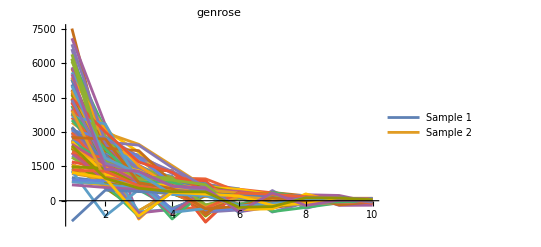

```mathematica
ListLinePlot[resultsList[[1,"AnalysisResult","SampledEvals"]],PlotRange->All,PlotLegends->Table["Sample "<>ToString[i],{i,2}],PlotLabel->resultsList[[1,"Name"]]]
```

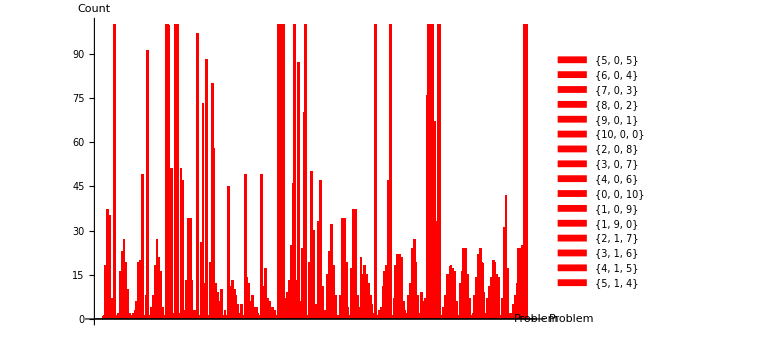

```mathematica
tallyData=Flatten[Map[Function[result,With[{name=result["Name"],tally=result["AnalysisResult","TallyIndices"]},Map[{name,First[#],Last[#]}&,tally]]],resultsList],1];

(*Convert pattern to a label and a saddle check*)
tallyDataLabeled=tallyData/. {name_,{p_,z_,n_},c_}:>{name,ToString[{p,z,n}],c,IsSaddleSignature[{p,z,n}]};

(*Extract unique patterns*)
patterns=DeleteDuplicates[tallyDataLabeled[[All,2]]];

BarChart[(*Heights of the bars*)tallyDataLabeled[[All,3]],ChartLabels->{tallyDataLabeled[[All,1]],None},ChartLayout->"Grouped",ChartLegends->patterns,ChartStyle->MapThread[(*If it's a saddle signature,highlight in a distinct color (e.g.Red)*)If[#2===True,Red,Automatic]&,{tallyDataLabeled[[All,2]],tallyDataLabeled[[All,4]]}],ImageSize->Large,AxesLabel->{"Problem","Count"},RotateLabel->True]
```

```mathematica
problemSaddleCounts=Association[GroupBy[tallyDataLabeled,First->Last[#]&,Total@Pick[#[[All,3]],#[[All,4]],True]&]];

(*This gives you an association:problemName->total count of saddle patterns*)
problemSaddleCounts

(*Sort to see which are richest in saddle points*)
sortedSaddleCounts=ReverseSortBy[problemSaddleCounts,Identity]

Grid[Prepend[Normal[KeyValueMap[{#1,#2}&,sortedSaddleCounts]],{"Problem","Total Saddle Count"}],Frame->All]
```

<|(First→True)→2417,(First→False)→0|>

<|(First→True)→2417,(First→False)→0|>

Problem | Total Saddle Count
First→True | 2417
First→False | 0

```mathematica
tallyData=Flatten[Map[Function[result,With[{name=result["Name"],tally=result["AnalysisResult","TallyIndices"]},Map[{name,First[#],Last[#]}&,tally]]],resultsList],1];

(*Convert pattern to a label and a saddle check*)
tallyDataLabeled=tallyData/. {name_,{p_,z_,n_},c_}:>{name,ToString[{p,z,n}],c,IsSaddleSignature[{p,z,n}]};

(*Extract unique patterns*)
patterns=DeleteDuplicates[tallyDataLabeled[[All,2]]];

BarChart[(*Heights of the bars*)tallyDataLabeled[[All,3]],ChartLabels->{tallyDataLabeled[[All,1]],None},ChartLayout->"Grouped",ChartLegends->patterns,ChartStyle->MapThread[(*If it's a saddle signature,highlight in a distinct color (e.g.Red)*)If[#2===True,Red,Automatic]&,{tallyDataLabeled[[All,2]],tallyDataLabeled[[All,4]]}],ImageSize->Large,AxesLabel->{"Problem","Count"},RotateLabel->True]
```

-Graphics-

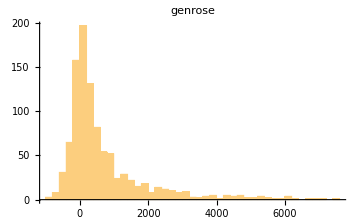
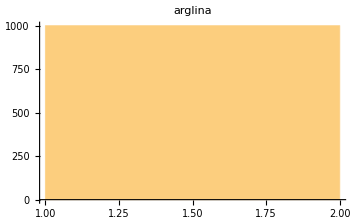
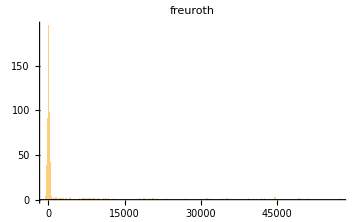
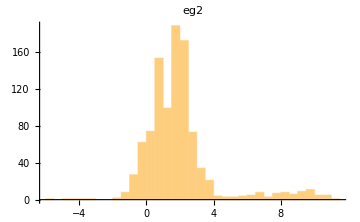
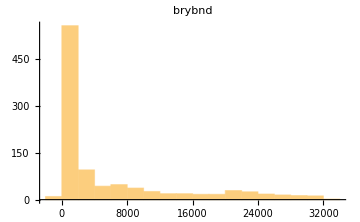
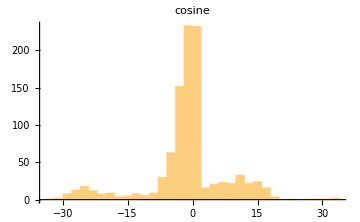
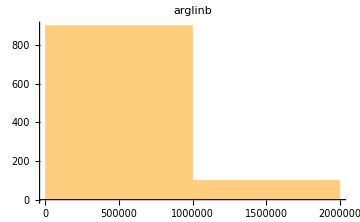
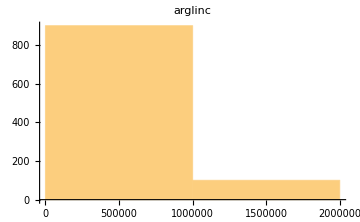
Style[genrose,None] | -Graphics-
Style[arglina,None] | -Graphics-
Style[freuroth,None] | -Graphics-
Style[eg2,None] | -Graphics-
Style[brybnd,None] | -Graphics-
Style[cosine,None] | -Graphics-
Style[arglinb,None] | -Graphics-
Style[arglinc,None] | -Graphics-
Style[argtrig,None] | -Graphics-
Style[arwhead,None] | -Graphics-
Style[bdqrtic,None] | -Graphics-
Style[brownal,None] | -Graphics-
Style[broyden3d,None] | -Graphics-
Style[brybnd,None] | -Graphics-
Style[chnrosnb_mod,None] | -Graphics-
Style[cragglvy,None] | -Graphics-
Style[cragglvy2,None] | -Graphics-
Style[curly10,None] | -Graphics-
Style[curly10,None] | -Graphics-
Style[curly20,None] | -Graphics-
Style[curly30,None] | -Graphics-
Style[dixon3dq,None] | -Graphics-
Style[dqdrtic,None] | -Graphics-
Style[dqrtic,None] | -Graphics-
Style[edensch,None] | -Graphics-
Style[eg2,None] | -Graphics-
Style[engval1,None] | -Graphics-
Style[errinros_mod,None] | -Graphics-
Style[extrosnb,None] | -Graphics-
Style[fletcbv2,None] | -Graphics-
Style[fletcbv3_mod,None] | -Graphics-
Style[fletchcr,None] | -Graphics-
Style[freuroth,None] | -Graphics-
Style[genhumps,None] | -Graphics-
Style[genrose_nash,None] | -Graphics-
Style[indef_mod,None] | -Graphics-
Style[integreq,None] | -Graphics-
Style[liarwhd,None] | -Graphics-
Style[morebv,None] | -Graphics-
Style[noncvxu2,None] | -Graphics-
Style[noncvxun,None] | -Graphics-
Style[nondia,None] | -Graphics-
Style[nondquar,None] | -Graphics-
Style[penalty1,None] | -Graphics-
Style[penalty2,None] | -Graphics-
Style[penalty3,None] | -Graphics-
Style[power,None] | -Graphics-
Style[quartc,None] | -Graphics-
Style[sbrybnd,None] | -Graphics-
Style[schmvett,None] | -Graphics-
Style[scosine,None] | -Graphics-
Style[sinquad,None] | -Graphics-
Style[tointgss,None] | -Graphics-
Style[tquartic,None] | -Graphics-
Style[tridia,None] | -Graphics-
Style[vardim,None] | -Graphics-

```mathematica
(*Let's just annotate histograms for saddle-rich problems*)
highlightedProblems=Keys@Select[problemSaddleCounts,#>0&];
Monitor[Grid[Table[With[{problemName=resultsList[[i,"Name"]],vals=Flatten[resultsList[[i,"AnalysisResult","SampledEvals"]]]},{Style[problemName,If[MemberQ[highlightedProblems,problemName],Bold,None]],Show[Histogram[vals,PlotRange->All,ImageSize->Medium,PlotLabel->problemName],If[MemberQ[highlightedProblems,problemName],Graphics[{Red,Text["Saddle-Rich",Scaled[{0.7,0.9}]]}],{}]]}],{i,Length[resultsList]}],Frame->All],"Building annotated histograms..."]
```

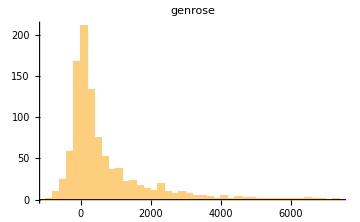
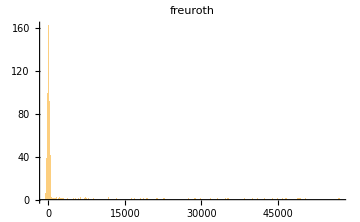
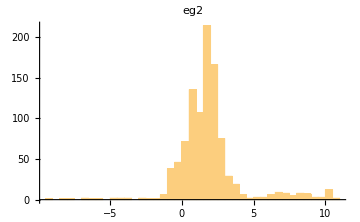
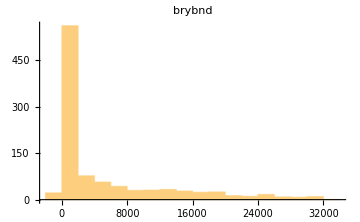
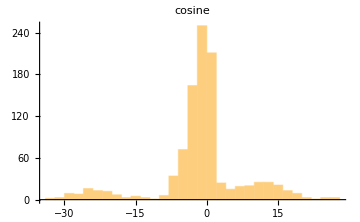
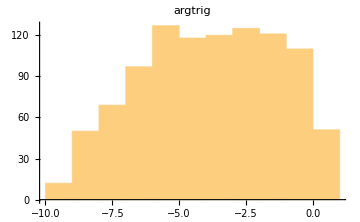
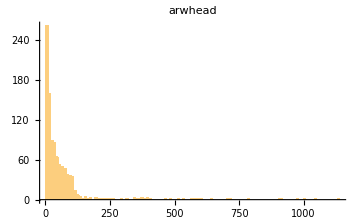
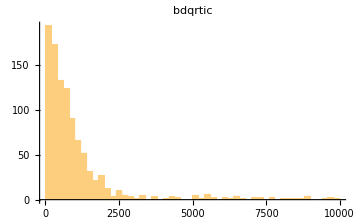
```mathematica
{{Style["genrose",None], -Graphics-}, {Style["arglina",None], -Graphics-}, {Style["freuroth",None], -Graphics-}, {Style["eg2",None], -Graphics-}, {Style["brybnd",None], -Graphics-}, {Style["cosine",None], -Graphics-}, {Style["arglinb",None], -Graphics-}, {Style["arglinc",None], -Graphics-}, {Style["argtrig",None], -Graphics-}, {Style["arwhead",None], -Graphics-}, {Style["bdqrtic",None], -Graphics-}, {Style["brownal",None], -Graphics-}, {Style["broyden3d",None], -Graphics-}, {Style["brybnd",None], -Graphics-}, {Style["chnrosnb_mod",None], -Graphics-}, {Style["cragglvy",None], -Graphics-}, {Style["cragglvy2",None], -Graphics-}, {Style["curly10",None], -Graphics-}, {Style["curly10",None], -Graphics-}, {Style["curly20",None], -Graphics-}, {Style["curly30",None], -Graphics-}, {Style["dixon3dq",None], -Graphics-}, {Style["dqdrtic",None], -Graphics-}, {Style["dqrtic",None], -Graphics-}, {Style["edensch",None], -Graphics-}, {Style["eg2",None], -Graphics-}, {Style["engval1",None], -Graphics-}, {Style["errinros_mod",None], -Graphics-}, {Style["extrosnb",None], -Graphics-}, {Style["fletcbv2",None], -Graphics-}, {Style["fletcbv3_mod",None], -Graphics-}, {Style["fletchcr",None], -Graphics-}, {Style["freuroth",None], -Graphics-}, {Style["genhumps",None], -Graphics-}, {Style["genrose_nash",None], -Graphics-}, {Style["indef_mod",None], -Graphics-}, {Style["integreq",None], -Graphics-}, {Style["liarwhd",None], -Graphics-}, {Style["morebv",None], -Graphics-}, {Style["noncvxu2",None], -Graphics-}, {Style["noncvxun",None], -Graphics-}, {Style["nondia",None], -Graphics-}, {Style["nondquar",None], -Graphics-}, {Style["penalty1",None], -Graphics-}, {Style["penalty2",None], -Graphics-}, {Style["penalty3",None], -Graphics-}, {Style["power",None], -Graphics-}, {Style["quartc",None], -Graphics-}, {Style["sbrybnd",None], -Graphics-}, {Style["schmvett",None], -Graphics-}, {Style["scosine",None], -Graphics-}, {Style["sinquad",None], -Graphics-}, {Style["tointgss",None], -Graphics-}, {Style["tquartic",None], -Graphics-}, {Style["tridia",None], -Graphics-}, {Style["vardim",None], -Graphics-}}problemSaddleCounts=\
```

```mathematica
ListLinePlot[resultsList[[1,"AnalysisResult","SampledEvals"]],PlotRange->All,PlotLegends->Table["Sample "<>ToString[i],{i,2}],PlotLabel->resultsList[[1,"Name"]]]
```

-Graphics-

TODO: Add figures/tables to display the results. Export resultsList to JSON.

### FindMinimum: Stationary Point Analysis

Run a lot of experiments. Use small abs_tol as we are concerned with the behavior of convergence iterations.
Decouple the FindMinimum routine from above.

```mathematica
(*		"FindMinimum" ->  findMinimum,*)
(* Run FindMinimum on the function f starting at x0 *)
findMinimum = Quiet[
FindMinimum[
	f[vars], 
		Evaluate[Thread[{vars, x0}]]
	]
]
```

FindMinimum[f[vars],{{vars,0.333333},{vars,0.666667}}]